# title

Abstract

## Key Concepts

x

x

x

## Statement of the Deutsch-Jozsa Problem

Let’s consider the 3^rd Boolean function in 3 variables.

```mathematica
boo=BooleanFunction[3,3]
```

BooleanFunction[…]

```mathematica
#->boo@@#&/@Tuples[{0,1},3]
```

{{0,0,0}→True,{0,0,1}→True,{0,1,0}→False,{0,1,1}→False,{1,0,0}→False,{1,0,1}→False,{1,1,0}→False,{1,1,1}→False}

For the Deutsch-Jozsa algorithm, the goal is to determine whether a Boolean function is constant (producing the same output regardless of the input, either 0 or 1) or balanced (yielding an equal number of 0s and 1s).

Define a balanced Boolean function:

```mathematica
bf=BooleanFunction[2,2];
BooleanConvert[bf][x,y]
```

!x&&y

Show its Boolean table (note same number of True and False)

```mathematica
BooleanTable[bf]
```

{False,False,True,False}

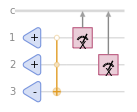

```mathematica
QuantumCircuitOperator["DeutschJozsa"[bf]]["Diagram"]
```

One can also get the Deutsch-Jozsa with a Phase oracle:

```mathematica
QuantumCircuitOperator["DeutschJozsaPhase"[bf]]["Diagram"]
```

-Graphics-

Also, “DeutschJozsaPhase” can take two integers, with the first one k+1 and second one as n, where the Boolean function is defined as BooleanFunction[k,n]

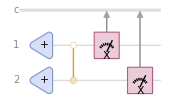

```mathematica
QuantumCircuitOperator["DeutschJozsaPhase"[3,2]]["Diagram"]
```

Given all Boolean functions with two variables, show number of True and False in their solutions, and also corresponding Deutsch-Jozsa probabilities:

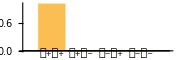
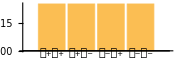
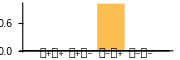
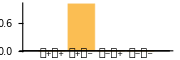
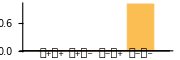
Boolean function | True | False | Deutsch-Jozsa probabilities
False | 0 | 4 | -Graphics-
!x&&!y | 1 | 3 | -Graphics-
!x&&y | 1 | 3 | -Graphics-
!x | 2 | 2 | -Graphics-
x&&!y | 1 | 3 | -Graphics-
!y | 2 | 2 | -Graphics-
(x&&!y)||(!x&&y) | 2 | 2 | -Graphics-
!x||!y | 3 | 1 | -Graphics-
x&&y | 1 | 3 | -Graphics-
(x&&y)||(!x&&!y) | 2 | 2 | -Graphics-
y | 2 | 2 | -Graphics-
!x||y | 3 | 1 | -Graphics-
x | 2 | 2 | -Graphics-
x||!y | 3 | 1 | -Graphics-
x||y | 3 | 1 | -Graphics-
True | 4 | 0 | -Graphics-

```mathematica
Grid[Prepend[Table[With[{bf=BooleanFunction[f,2]},{BooleanConvert[bf][x,y],Count[True][BooleanTable[bf]],Count[False][BooleanTable[bf]],With[{rs=QuantumCircuitOperator["DeutschJozsa"[bf]][]["Probabilities"]},BarChart[rs,ChartLabels->Keys[rs],AspectRatio->1/3,ImageSize->Small]]}],{f,0,15}],Style[#,Bold]&/@{"Boolean function","True","False","Deutsch-Jozsa probabilities"}],Frame->All,Alignment->{{Left,Center,Center,Center}}]
```

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]